```mathematica
$Assumptions = Im[α]==0&&Im[γ]==0&&Im[y]==0&&Im[θ]==0;
```

```mathematica
F1[α_,γ_,θ_]:=NIntegrate[y BesselJ[0,α y θ] (Exp[ⅈ Sqrt[Pi] γ/α Exp[-y^2]]-1),{y,0,∞},Method->{"DoubleExponentialOscillatory","SymbolicProcessing"->0}];
```

```mathematica
F2[α_,γ_,θ_]:= γ^2 Pi/4 Exp[-2α^2 Sin[θ/2]^2];
```

```mathematica
F3[α_,γ_,θ_]:= α^2*F1[α,γ,θ]*Conjugate[F1[α,γ,θ]];
```

```mathematica
PP[α_,γ_]:=Plot[{F2[α,γ,θ],F3[α,γ,θ]},{θ,0, Pi},PlotLegends->{"Born","Eikonel"},PlotRange->All,AxesLabel->{"θ","(|f (θ)SuperscriptBox[|, 2])/r_0^2"},PlotLabel->StringJoin["α=",ToString[α],"  γ=",ToString[γ]]];
```

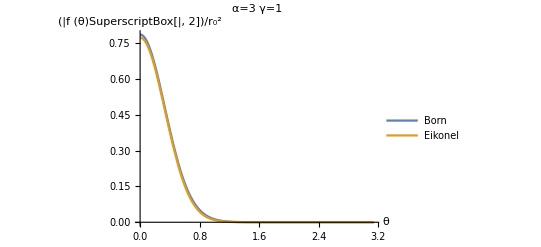

```mathematica
PP[3,1]
```